```mathematica
获取帮助：
	1、从列表中选一个
	  2、输入一个命令的名字或者在查询栏查询
	3、使用"？命令"可以查看函数帮助
命令执行：shift+enter
单元：Mathematica计算的最小单元，当光标从竖直变为水平的地方开启新的单元，
	单元是可以嵌套的，同一个输入和输出输出属于同一个单元
```

```mathematica
2+2
```

4

```mathematica
四则运算：Mathematica可以精确的对数字进行四则运算
```

```mathematica
123^45
```

11110408185131956285910790587176451918559153212268021823629073199866111001242743283966127048043

```mathematica
115/39+727/119
```

42038/4641

```mathematica
Mathematica内置常用三角函数，对数函数，指数函数，平方根函数等基本函数，还有像π,e这样的常量,Pi作为π的内置常量
```

```mathematica
Sin[π/4] ;Sin[Pi/4]
```

1/(√2)

```mathematica
Sin[Pi/4.0]
```

0.707107

```mathematica
上面两个例子中，第一个例子使用的是整数4，所以获得的结果是精确值，而第二个例子使用的浮点数4.0，所以获得的结果是一个近似的浮点值，也就是说，当表达式中都是精确的整数值时，会得出精确的结果，当表达式中含有浮点数时，会得出近似的结果
```

```mathematica
2*x-2x
```

0

```mathematica
Mathematica同样支持多步计算：
	1、我们可以使用"%"来代表上一个计算的结果例如：
```

```mathematica
119/11+47/13
```

2064/143

```mathematica
%-107/23
```

32171/3289

```mathematica
2、为了引用比较早的结果，可以使用"Out"关键字，例如
```

```mathematica
Out[8]
```

0.707107

```mathematica
3、我们可以使用"%%"表示倒数第二个输出
```

```mathematica
%%
```

12+12 x-x^2/2-x^3/6

```mathematica
我们可以通过N函数将分数转换为浮点数，同样可以指定小数位数
```

```mathematica
129/9
```

43/3

```mathematica
N[%]
```

14.3333

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

其他一些小功能，例如计算全文档，格式化文本，单元格的显示和隐藏，双击右边的边界符

```mathematica
定义函数功能，注意为了避免符号出现问题，我们可以使用ClearAll[]函数清楚符号的引用
```

```mathematica
ClearAll[u,t,a]
u[t_]=E^(a*t)
```

ⅇ^(a t)

```mathematica
函数定义需要注意的地方
1、函数定义使用方括号[],即使用f[x_]来定义函数
2、参数需要使用下划线结尾,下划线是将符号定义进行清除
3、需要多个函数，新的函数需要换新行
4、函数定义形式参数不使用下划线x_结尾，则将之看为定义单个函数值的定义
```

```mathematica
ClearAll[g]
g[x]=x^2
```

x^2

```mathematica
g[2]
g[x]
```

g[2]

x^2

```mathematica
u[5]
```

ⅇ^(5 a)

```mathematica
D[u[t],t]
```

a ⅇ^(a t)

```mathematica
ClearAll[w,x,y]
w[x_,y_]=Sin[x*Pi]+Sin[Pi*y]
```

Sin[π x]+Sin[π y]

```mathematica
D[w[x,y],x,x]+D[w[x,y],y,y]
```

-π^2 Sin[π x]-π^2 Sin[π y]

```mathematica
D[w[x,y],{y,5}]
```

π^5 Cos[π y]

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

```mathematica
ClearAll[g]
g[x_]=x^2
```

x^2

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
Mathematica可以计算明确或者不明确的积分,也可以计算数值积分
```

```mathematica
Integrate[Sin[x],x]
Integrate[Sin[x],{x,0,1}]
NIntegrate[E^Cos[x],{x,0,1}]
```

-Cos[x]

1-Cos[1]

2.34157

```mathematica
解二次积分
(-d^2 u)/(d^2 x)=1+x,0<x<1,u(0)=0,u(1)=(0).
```

```mathematica
ClearAll[u,x,a,b]
Integrate[-(x+1),x]+a
```

a-x-x^2/2

```mathematica
Integrate[%,x]+b
```

b+a x-x^2/2-x^3/6

```mathematica
u[x_]=%
```

b+a x-x^2/2-x^3/6

```mathematica
Solve[{u[0]==0,u[1]==0},{a,b}]
```

{{a→2/3,b→0}}

```mathematica
u[x]
```

b+a x-x^2/2-x^3/6

```mathematica
a=12
b=12
```

12

12

```mathematica
u[x]
```

12+12 x-x^2/2-x^3/6

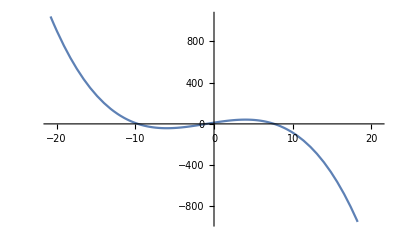

```mathematica
Plot[12+12 x-x^2/2-x^3/6,{x,-20.784609690826528,20.784609690826528}]
```

```mathematica
化简结果
```

```mathematica
Simplify[s]
```

s

```mathematica
绘图功能：Plot
```

```mathematica
ClearAll[C1,C2]
Integrate[C1/(1+x/2),x]+C2
```

C2+2 C1 Log[2+x]

```mathematica
u[x_]=%
```

C2+2 C1 Log[2+x]

```mathematica
Solve[{u[0]==20,u[1]==25},{C1,C2}]
```

{{C1→-5/(2 (Log[2]-Log[3])),C2→(5 (5 Log[2]-4 Log[3]))/(Log[2]-Log[3])}}

```mathematica
u[x]
```

C2+2 C1 Log[2+x]

```mathematica
C1=-5/(2(Log[2]-Log[3]))
C2=5(5Log[2]-4Log[3])/(Log[2]-Log[3])
```

-5/(2 (Log[2]-Log[3]))

(5 (5 Log[2]-4 Log[3]))/(Log[2]-Log[3])

```mathematica
u[x]
```

(5 (5 Log[2]-4 Log[3]))/(Log[2]-Log[3])-(5 Log[2+x])/(Log[2]-Log[3])

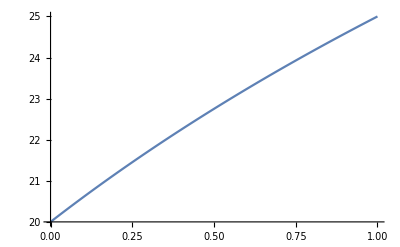

```mathematica
Plot[u[x],{x,1,0}]
```

```mathematica
Plot[u[x],{x,0,1},PlotRange->{20,25}]
```

-Graphics-

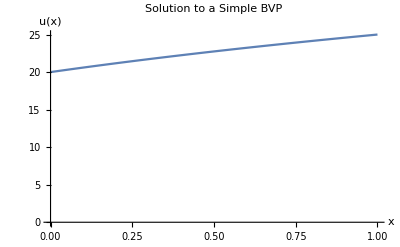

```mathematica
Plot[u[x],{x,0,1},PlotRange->{0,25},AxesLabel->{"x","u(x)"},PlotLabel->"Solution to a Simple BVP"]
```

```mathematica
基本线性代数：
```

```mathematica
ClearAll[x]
x={1,2,3}
```

{1,2,3}

```mathematica
MatrixForm[x]
```

(1
2
3)

```mathematica
x//MatrixForm
```

(1
2
3)

```mathematica
ClearAll[A]
A={{1,2,-1},{4,2,3},{4,4,5}}
A//MatrixForm
```

{{1,2,-1},{4,2,3},{4,4,5}}

(1 | 2 | -1
4 | 2 | 3
4 | 4 | 5)

```mathematica
Transpose[A]//MatrixForm
```

(1 | 4 | 4
2 | 2 | 4
-1 | 3 | 5)

```mathematica
A.A
```

{{5,2,0},{24,24,17},{40,36,33}}

```mathematica
A.x
```

{2,17,27}

```mathematica
矩阵操作：Transpose 转置 MatrixForm 矩阵格式化 ，使用方括号x[[2]]来代表下标,可以使用All关键字
```

```mathematica
x[[2]]
```

2

```mathematica
A[[2]]
```

{4,2,3}

```mathematica
A[[All,2]]
```

{2,2,4}

```mathematica
Ax=b解的唯一性,零空间Ax=0时x的解，如果有唯一0解，则称之为非奇异矩阵，否则无穷解，则为奇异矩阵，奇异矩阵的非零度空间有无穷解或无解，非奇异矩阵有唯一解。基：有限个向量张成线性空间，且本身线性无关，
```

```mathematica
ClearAll[B]
B={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
NullSpace[B]
```

{{1,-2,1}}

```mathematica
y=%%[[1]]
```

{1,-2,1}

```mathematica
NullSpace[A]
```

{}

```mathematica
A//MatrixForm
```

(1 | 2 | -1
4 | 2 | 3
4 | 4 | 5)

```mathematica
基和维数
```

```mathematica
ClearAll[v1,v2,v3]
v1={1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}
v2={1/Sqrt[2],0,-1/Sqrt[2]}
v3={1/Sqrt[6],-2/Sqrt[6],1/Sqrt[6]}
```

{1/(√3),1/(√3),1/(√3)}

{1/(√2),0,-1/(√2)}

{1/(√6),-√(2/3),1/(√6)}

```mathematica
v1.v2
v2.v3
v1.v3
```

0

0

0

```mathematica
ClearAll[p1,p2,p3,x]
p1[x_]=1
p2[x_]=x-1/2
p3[x_]=x^2-x+1/6
```

1

-1/2+x

1/6-x+x^2

```mathematica
ClearAll[a,b,c,q,x]
q[x_]=ax^2+bx+c
```

ax^2+bx+c

```mathematica
ClearAll[c1,c2,c3]
q[x]-(c1 p1[x]+c2 p2[x]+c3 p3[x])
```

ax^2+bx+c-c1-c2 (-1/2+x)-c3 (1/6-x+x^2)

```mathematica
Collect[%, x ]
```

ax^2+bx+c-c1+c2/2-c3/6+(-c2+c3) x-c3 x^2

```mathematica
Solve[{Coefficient[%,x,0]==0,Coefficient[%,x,1]==0,Coefficient[%,x,2]==0},{c1 ,c2 ,c3 }]
```

{{c1→ax^2+bx+c,c2→0,c3→0}}

```mathematica
x^2+3x+1 /.x->3
```

19

```mathematica
可以通过符号"/."求取参数取特定值的时候函数的值
```

```mathematica
ClearAll[x,y]
x^2y/.{x->2,y->-4}
```

-16

```mathematica
Solve[x^2-3x+3==0,x]
```

{{x→1/2 (3-ⅈ √3)},{x→1/2 (3+ⅈ √3)}}

```mathematica
ClearAll[x,y,sols]
```

```mathematica
sols=Solve[{x^2+y^2==1,y==x},{x,y}]
```

{{x→-1/(√2),y→-1/(√2)},{x→1/(√2),y→1/(√2)}}

```mathematica
x+y/.sols[[1]]
```

-√2